0.000307929-1.91737951895799×10^-1409 ⅈ

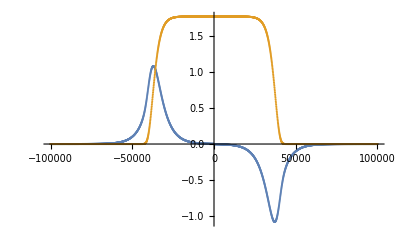

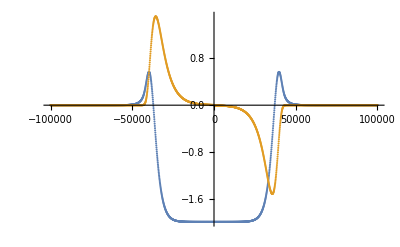

/Users/dg6/code/kineticj/mathematica

```mathematica
Z[re_,im_,sgnKprl_]:= If[sgnKprl≥0,I Sqrt[Pi] Exp[-(re+ I im)^2] Erfc[-I (re+I im)],-I Sqrt[Pi] Exp[-(-1(re+ I im))^2] Erfc[-I (-1(re+I im))]];
Zp[re_,im_,sgnKprl_]:=If[sgnKprl≥0,-2 (1+(re+I im) Z[re,im,sgnKprl]),-2 (1-(re+I im) (-1Z[re,im,sgnKprl]))];
zReMin=-100000;zReMax=100000;nPtsRe=2000;
zRe=N[Table[re,{re,zReMin,zReMax,(zReMax-zReMin)/(nPtsRe-1)}]];
argMin=0.001;argMax=100000;argN=1000;
zReNonUniform=N[Table[10^(i/(argN-1)*(Log10[argMax]-Log10[argMin])+Log10[argMin]),{i,0,argN-1}]];
zReNonUniform1=Prepend[zReNonUniform,0];
zReNonUniform2=Join[-Reverse[zReNonUniform],zReNonUniform1];
ZData=Z[zReNonUniform2,0,1];
ZPData=Zp[zReNonUniform2,0,1];
Zp[57.0,0,1]
ListPlot[{Re[ZData],Im[ZData]},DataRange->{zReMin,zReMax}]
ListPlot[{Re[ZPData],Im[ZPData]},DataRange->{zReMin,zReMax}]
SetDirectory["~/code/kineticj/mathematica"]
Export["zFunction.nc",{"arg_re"->zReNonUniform2, "Z_re"->Re[ZData], "Z_im"->Im[ZData], "Zp_re"->Re[ZPData],"Zp_im"->Im[ZPData]}];(*,"Zp_re"->Re[ZPData],"Zp_im"->Im[ZPData]}];*)
(*Export["zFunction_kPrl_p.nc",{zRe,Re[ZData],Im[ZData],Re[ZPData],Im[ZPData]},{"Datasets",{"arg_re","Z_re","Z_im","Zp_re","Zp_im"}}];
ZData=Z[zRe,0,-1];
ZPData=Zp[zRe,0,-1];
ListPlot[{Re[ZData],Im[ZData]},DataRange->{zReMin,zReMax}]
ListPlot[{Re[ZPData],Im[ZPData]},DataRange->{zReMin,zReMax}]
Export["zFunction_kPrl_n.nc",{zRe,Re[ZData],Im[ZData],Re[ZPData],Im[ZPData]},{"Datasets",{"arg_re","Z_re","Z_im","Zp_re","Zp_im"}}];*)
```